```mathematica
signconfig1 = {1,1,1,1,-1,-1,-1,-1}
```

{1,1,1,1,-1,-1,-1,-1}

```mathematica
H={{0,t1,0,0,0,0,0,t2},{t1,0,t2,0,ⅇ^(ⅈ k2) t1,0,0,0},{0,t2,0,t1,0,0,0,ⅇ^(ⅈ k1) t1},{0,0,t1,0,t2,0,ⅇ^(ⅈ k1) t1,0},{0,ⅇ^(-ⅈ k2) t1,0,t2,0,t1,0,0},{ⅇ^(-ⅈ k2) t1,0,0,0,t1,0,t2,0},{0,0,0,ⅇ^(-ⅈ k1) t1,0,t2,0,t1},{t2,0,ⅇ^(-ⅈ k1) t1,0,0,0,t1,0}}
```

{{0,t1,0,0,0,0,0,t2},{t1,0,t2,0,ⅇ^(ⅈ k2) t1,0,0,0},{0,t2,0,t1,0,0,0,ⅇ^(ⅈ k1) t1},{0,0,t1,0,t2,0,ⅇ^(ⅈ k1) t1,0},{0,ⅇ^(-ⅈ k2) t1,0,t2,0,t1,0,0},{ⅇ^(-ⅈ k2) t1,0,0,0,t1,0,t2,0},{0,0,0,ⅇ^(-ⅈ k1) t1,0,t2,0,t1},{t2,0,ⅇ^(-ⅈ k1) t1,0,0,0,t1,0}}

```mathematica
HH=DiagonalMatrix[δ signconfig1]+H
```

{{δ,t1,0,0,0,0,0,t2},{t1,δ,t2,0,ⅇ^(ⅈ k2) t1,0,0,0},{0,t2,δ,t1,0,0,0,ⅇ^(ⅈ k1) t1},{0,0,t1,δ,t2,0,ⅇ^(ⅈ k1) t1,0},{0,ⅇ^(-ⅈ k2) t1,0,t2,-δ,t1,0,0},{ⅇ^(-ⅈ k2) t1,0,0,0,t1,-δ,t2,0},{0,0,0,ⅇ^(-ⅈ k1) t1,0,t2,-δ,t1},{t2,0,ⅇ^(-ⅈ k1) t1,0,0,0,t1,-δ}}

```mathematica
With[{t1=1,t2=0.8,δ=0.1,k1=0},Plot[Sort[Re[Eigenvalues[N[HH]]]]]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[Sort[Re[Eigenvalues[N[HH]]]]]

```mathematica
With[{t1=1,t2=0.8,δ=0.1,k2=0},Plot[Sort[Re[Eigenvalues[N[HH]]]],{k1,-π,π}]]
```

```mathematica
H[t1_,t2_,k1_,k2_]={0,t1,0,0,0,0,0,t2},{t1,0,t2,0,ⅇ^(ⅈ k2) t1,0,0,0},{0,t2,0,t1,0,0,0,ⅇ^(ⅈ k1) t1},{0,0,t1,0,t2,0,ⅇ^(ⅈ k1) t1,0},{0,ⅇ^(-ⅈ k2) t1,0,t2,0,t1,0,0},{ⅇ^(-ⅈ k2) t1,0,0,0,t1,0,t2,0},{0,0,0,ⅇ^(-ⅈ k1) t1,0,t2,0,t1},{t2,0,ⅇ^(-ⅈ k1) t1,0,0,0,t1,0}}
```

```mathematica
HH=DiagonalMatrix[δ signconfig1]+H
```

H+DiagonalMatrix[signconfig1 δ]

```mathematica
HH
```

H+DiagonalMatrix[signconfig1 δ]

```mathematica
HH=DiagonalMatrix[δ*signconfig1]+H
```

H+DiagonalMatrix[signconfig1 δ]

```mathematica
H[t1_,t2_,k1_,k2_]:={{0,t1,0,0,0,0,0,t2},{t1,0,t2,0,ⅇ^(ⅈ k2) t1,0,0,0},{0,t2,0,t1,0,0,0,ⅇ^(ⅈ k1) t1},{0,0,t1,0,t2,0,ⅇ^(ⅈ k1) t1,0},{0,ⅇ^(-ⅈ k2) t1,0,t2,0,t1,0,0},{ⅇ^(-ⅈ k2) t1,0,0,0,t1,0,t2,0},{0,0,0,ⅇ^(-ⅈ k1) t1,0,t2,0,t1},{t2,0,ⅇ^(-ⅈ k1) t1,0,0,0,t1,0}}+DiagonalMatrix[δ*signconfig1]
```

```mathematica
H[t1,0.8*t1,k1,k2]
```

{{δ,t1,0,0,0,0,0,0.8 t1},{t1,δ,0.8 t1,0,ⅇ^(ⅈ k2) t1,0,0,0},{0,0.8 t1,δ,t1,0,0,0,ⅇ^(ⅈ k1) t1},{0,0,t1,δ,0.8 t1,0,ⅇ^(ⅈ k1) t1,0},{0,ⅇ^(-ⅈ k2) t1,0,0.8 t1,-δ,t1,0,0},{ⅇ^(-ⅈ k2) t1,0,0,0,t1,-δ,0.8 t1,0},{0,0,0,ⅇ^(-ⅈ k1) t1,0,0.8 t1,-δ,t1},{0.8 t1,0,ⅇ^(-ⅈ k1) t1,0,0,0,t1,-δ}}

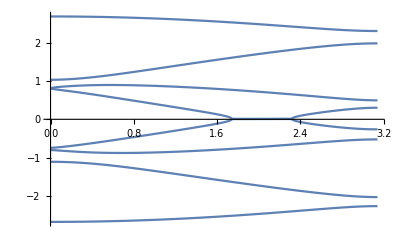

```mathematica
With[{t1=1,δ=0.1,k2=0},Plot[Sort[Re[Eigenvalues[N[{{δ,t1,0,0,0,0,0,0.8 t1},{t1,δ,0.8 t1,0,ⅇ^(ⅈ k2) t1,0,0,0},{0,0.8 t1,δ,t1,0,0,0,ⅇ^(ⅈ k1) t1},{0,0,t1,δ,0.8 t1,0,ⅇ^(ⅈ k1) t1,0},{0,ⅇ^(-ⅈ k2) t1,0,0.8 t1,-δ,t1,0,0},{ⅇ^(-ⅈ k2) t1,0,0,0,t1,-δ,0.8 t1,0},{0,0,0,ⅇ^(-ⅈ k1) t1,0,0.8 t1,-δ,t1},{0.8 t1,0,ⅇ^(-ⅈ k1) t1,0,0,0,t1,-δ}}]]]],{k1,0,π}]]
```

```mathematica
HH=DiagonalMatrix[δ*signconfig1]+H
```

H+DiagonalMatrix[signconfig1 δ]

```mathematica
signconfig1 = {1,1,1,1,-1,-1,-1,-1}
```

{1,1,1,1,-1,-1,-1,-1}

```mathematica
HH=DiagonalMatrix[δ*signconfig1]+H
```

{{H+δ,H,H,H,H,H,H,H},{H,H+δ,H,H,H,H,H,H},{H,H,H+δ,H,H,H,H,H},{H,H,H,H+δ,H,H,H,H},{H,H,H,H,H-δ,H,H,H},{H,H,H,H,H,H-δ,H,H},{H,H,H,H,H,H,H-δ,H},{H,H,H,H,H,H,H,H-δ}}

```mathematica
H
```

H

```mathematica
H[t1_,t2_,k1_,k2_]={{0,t1,0,0,0,0,0,t2},{t1,0,t2,0,ⅇ^(ⅈ k2) t1,0,0,0},{0,t2,0,t1,0,0,0,ⅇ^(ⅈ k1) t1},{0,0,t1,0,t2,0,ⅇ^(ⅈ k1) t1,0},{0,ⅇ^(-ⅈ k2) t1,0,t2,0,t1,0,0},{ⅇ^(-ⅈ k2) t1,0,0,0,t1,0,t2,0},{0,0,0,ⅇ^(-ⅈ k1) t1,0,t2,0,t1},{t2,0,ⅇ^(-ⅈ k1) t1,0,0,0,t1,0}}
```

{{0,t1,0,0,0,0,0,t2},{t1,0,t2,0,ⅇ^(ⅈ k2) t1,0,0,0},{0,t2,0,t1,0,0,0,ⅇ^(ⅈ k1) t1},{0,0,t1,0,t2,0,ⅇ^(ⅈ k1) t1,0},{0,ⅇ^(-ⅈ k2) t1,0,t2,0,t1,0,0},{ⅇ^(-ⅈ k2) t1,0,0,0,t1,0,t2,0},{0,0,0,ⅇ^(-ⅈ k1) t1,0,t2,0,t1},{t2,0,ⅇ^(-ⅈ k1) t1,0,0,0,t1,0}}

```mathematica
HH=DiagonalMatrix[δ*signconfig1]+H
```

{{H+δ,H,H,H,H,H,H,H},{H,H+δ,H,H,H,H,H,H},{H,H,H+δ,H,H,H,H,H},{H,H,H,H+δ,H,H,H,H},{H,H,H,H,H-δ,H,H,H},{H,H,H,H,H,H-δ,H,H},{H,H,H,H,H,H,H-δ,H},{H,H,H,H,H,H,H,H-δ}}

```mathematica
signconfig1 = {1,1,1,1,-1,-1,-1,-1}
```

{1,1,1,1,-1,-1,-1,-1}

```mathematica
H[t1_,t2_,k1_,k2_]={{0,t1,0,0,0,0,0,t2},{t1,0,t2,0,ⅇ^(ⅈ k2) t1,0,0,0},{0,t2,0,t1,0,0,0,ⅇ^(ⅈ k1) t1},{0,0,t1,0,t2,0,ⅇ^(ⅈ k1) t1,0},{0,ⅇ^(-ⅈ k2) t1,0,t2,0,t1,0,0},{ⅇ^(-ⅈ k2) t1,0,0,0,t1,0,t2,0},{0,0,0,ⅇ^(-ⅈ k1) t1,0,t2,0,t1},{t2,0,ⅇ^(-ⅈ k1) t1,0,0,0,t1,0}}
```

{{0,t1,0,0,0,0,0,t2},{t1,0,t2,0,ⅇ^(ⅈ k2) t1,0,0,0},{0,t2,0,t1,0,0,0,ⅇ^(ⅈ k1) t1},{0,0,t1,0,t2,0,ⅇ^(ⅈ k1) t1,0},{0,ⅇ^(-ⅈ k2) t1,0,t2,0,t1,0,0},{ⅇ^(-ⅈ k2) t1,0,0,0,t1,0,t2,0},{0,0,0,ⅇ^(-ⅈ k1) t1,0,t2,0,t1},{t2,0,ⅇ^(-ⅈ k1) t1,0,0,0,t1,0}}